```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Equations use normalized parmaters τ=Subscript[ω, c] t, a = I/Subscript[I, c] and Mc Cumber - Stweart parameter Subscript[β, c]=0 (Heavily overdamped)
Procedure to obtain IV curve: 

1) Solve the equation for for phase ϕ[t] (define parametric function ysol)
     2) Evaluate voltage as derivative of ϕ[t] : (∂ϕ[t])/(∂t) 
	3) Evaluate time average of (∂ϕ[t])/(∂t) with NIntegrate (classical definition of <f> =1/T∫_0^T f[t]ⅆt)  over a period of about T = 150 t
			4) Plot IV curve as couple of poi ts [a,1/T∫_0^T (∂ϕ[t])/(∂t)ⅆt]
```

```mathematica
I also plotted  (∂ϕ[t])/(∂t) and ϕ[t]at varying of time to see oscillations
```

```mathematica
Sinusoidal current phase relationship
```

```mathematica
ysol2=ParametricNDSolveValue[{a==Sin[ϕ[t]]+ϕ'[t],ϕ[0]==k},ϕ,{t,0,1000},{a,k}]
```

ParametricFunction[<>]

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[NIntegrate[ND[ysol2[a,0][t],t,x], {x, 5, 5+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->10]/(2*Pi*((√(a^2-1))^-1)),{a,1.0000001,3},PlotRange->{{0,3},{0,3}}]//AbsoluteTiming
```

$Aborted

```mathematica
FullSimplify[DSolve[{a==Sin[ϕ[t]]+ϕ'[t],ϕ[0]==0},ϕ[t],t]]
```

{{ϕ[t]→2 ArcTan[(1+√(-1+a^2) Tan[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]])/a]}}

```mathematica
ϕ[t_,a_,k_]:=2 ArcTan[(1+√(-1+a^2) Tan[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]])/a]
```

```mathematica
A[t_,a_,k_]:=((-1+a^2) Sec[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]]^2)/(a (1+((1+√(-1+a^2) Tan[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]])^2)/a^2))
```

```mathematica
D[ϕ[t,a,k],t]
```

```mathematica
((-1+a^2) Sec[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]]^2)/(a (1+((1+√(-1+a^2) Tan[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]])^2)/a^2))
```

((-1+a^2) Sec[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]]^2)/(a (1+((1+√(-1+a^2) Tan[1/2 √(-1+a^2) t-ArcCot[√(-1+a^2)]])^2)/a^2))

```mathematica
Limit[ϕ[t,1.6,0]/t,t->Infinity]
```

0.

```mathematica
Manipulate[Plot[{A[t,a,k],ϕ[t,a,k]},{t,0,10*Pi},PlotRange->All],{a,0.0001,5}]
```

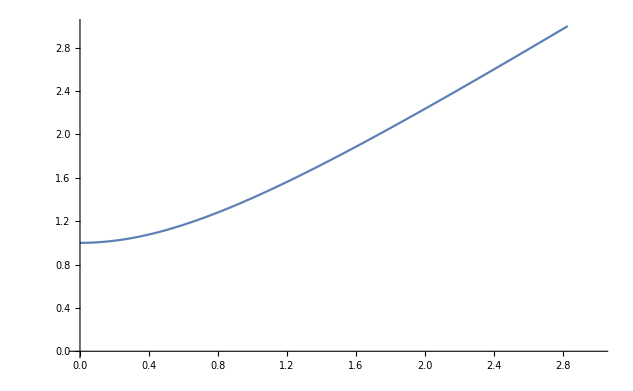
{0.678037,-Graphics-}

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[{NIntegrate[A[t,a,0], {t, 10, 10+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->20]/(2*Pi*((√(a^2-1))^-1))},{a,1,3},PlotRange->{{0,3},{0,3}}]//axisFlip//AbsoluteTiming
```

```mathematica
Manipulate[Plot[{2*(SawtoothWave[(x/b)-c]-d)},{x,-8/Pi,8/Pi},PlotRange->All],{b,0.1,50},{c,0,2},{d,0,3}]
```

```mathematica
Sawtooth defined in analytical way function
```

```mathematica
trg[x_,δ_]:=1-2 ArcCos[(1-δ) Sin[2 π x]]/π;
sqr[x_,δ_]:=2 ArcTan[Sin[2 π x]/δ]/π;
swt[x_,m_,δ_,t_]:=(t)*((1+trg[(2 x-1)/4,δ] sqr[x/2,δ])-m)


Manipulate[Plot[{Sin[x],2*SawtoothWave[((x/e))-b]-m,swt[((x/e))-b,m,δ,t],},{x,-8,8},PlotRange->All,Exclusions->None],{m,-8,8},{b,0,8},{e,0.01,10},{t,0.1,10},{δ,0.0001,1}]
```

```mathematica
FindMaximum[swt[((x/(2*Pi)))-0.5,1,0.005,1.133575],{x,0}]
```

{1.,{x→2.9706}}

```mathematica
Sawtooth defined in analytical way current phase relationship
```

```mathematica
ysol4=ParametricNDSolveValue[{a==(swt[((ϕ[t]/(2*Pi)))-0.5,1,0.005,1.133575])+ϕ'[t],ϕ[0]==k},ϕ,{t,0,1000},{a,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol4[a,k][t],t,x],ND[ysol2[a,k][t],t,x],ND[ysol6[a,l][t],t,x]}, {x, 0.0001,20},PlotRange->All,PlotLegends->{"smoot swt","Sin","L inductance"}],{a,0.0001,20},{k,0,2*Pi},{l,0,2}]//AbsoluteTiming
```

{0.000670709,}

```mathematica
Sawtooth defined by mathematica current phase relationship
```

```mathematica
ysol3=ParametricNDSolveValue[{a==(2*(SawtoothWave[(ϕ[t]/(2*Pi))-0.5]-0.5))+ϕ'[t],ϕ[0]==k},ϕ,{t,0,1000},{a,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol3[a,k][t],t,x]},{x, 0.00001,20},PlotRange->All],{a,0.0001,20},{k,0,2*Pi}]
```

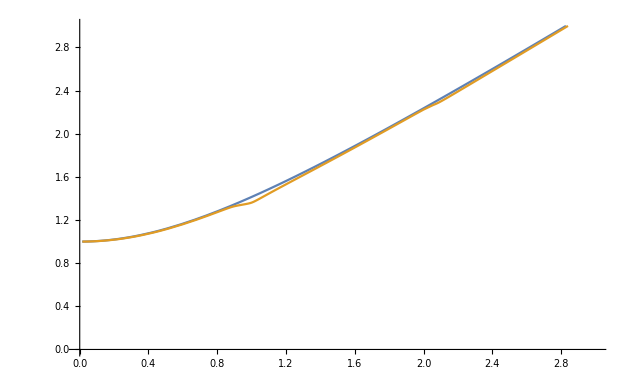

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[{NIntegrate[ND[ysol2[a,1,0][t],t,x], {x, 5, 5+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->10]/(2*Pi*((√(a^2-1))^-1)),NIntegrate[ND[ysol4[a,1,0][t],t,x], {x, 5, 5+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->20]/(2*Pi*((√(a^2-1))^-1))},{a,1.0001,3},PlotRange->{{0,3},{0,3}}]//axisFlip
```

```mathematica
Manipulate[Plot[TriangleWave[(x/b)],{x,-4,4},PlotRange->All],{b,0.1,50}]
```

```mathematica
TriangleWave[(Pi/(2Pi))]
```

0

```mathematica
triangular function (defined by mathematica) current phase relationship
```

```mathematica
ysol5=ParametricNDSolveValue[{a==TriangleWave[(ϕ[t]/(2*Pi))]+ϕ'[t],ϕ[0]==k},ϕ,{t,0,1000},{a,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol5[a,k][t],t,x],ND[ysol2[a,k][t],t,x],ND[ysol6[a,l][t],t,x]}, {x, 0,20},PlotRange->All,PlotLegends->{"tri","Sin","L inductance"}],{a,0.0001,20},{k,0,2*Pi},{l,0,2}]
```

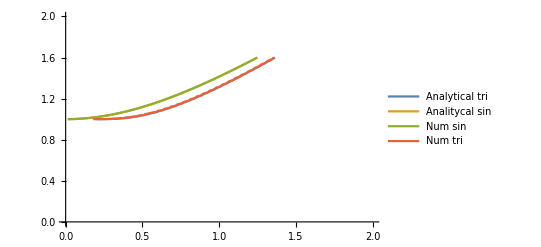
{5768.74,-Graphics-}

```mathematica
AbsoluteTiming[axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[{2*(Log[(a+1)/(a-1)])^(-1),NIntegrate[A[t,a,0], {t, 10, 10+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->20]/(2*Pi*((√(a^2-1))^-1)),NIntegrate[ND[ysol2[a,0][t],t,x], {x, 5, 5+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->10]/(2*Pi*((√(a^2-1))^-1)),NIntegrate[ND[ysol5[a,0][t],t,x], {x, 0, 150},MaxRecursion->20]/150},{a,1.0001,1.6},PlotRange->{{0,2},{0,2}},PlotLegends->{"Analytical tri", "Analitycal sin", "Num sin", "Num tri"}]//axisFlip]
```

```mathematica
N[NIntegrate[ND[ysol2[1.3,0][t],t,x], {x, 0, 100},MaxRecursion->20]/100]//AbsoluteTiming
```

{1.63755,0.828334}

```mathematica
N[NIntegrate[ND[ysol2[1.3,0][t],t,x], {x, 0, 100},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/100]//AbsoluteTiming
```

{0.632668,0.828334}

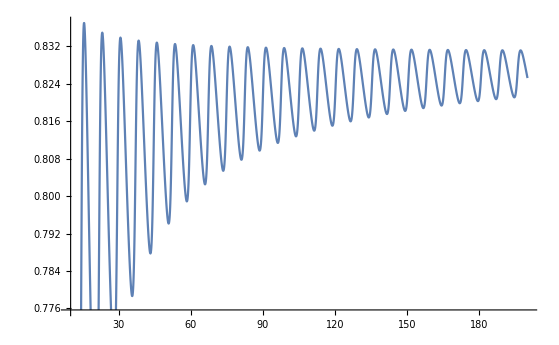
{1805.64,-Graphics-}

```mathematica
Plot[N[NIntegrate[ND[ysol2[1.3,0][t],t,x],{x, 0, g},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/g],{g,10,200}]//AbsoluteTiming
```

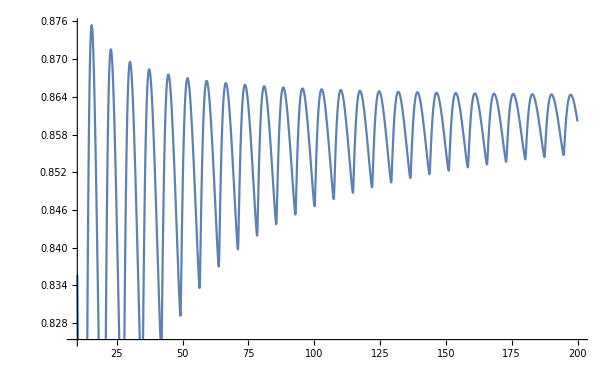
{1271.21,-Graphics-}

```mathematica
Plot[N[NIntegrate[ND[ysol4[1.3,0][t],t,x],{x, 0, g},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/g],{g,10,200}]//AbsoluteTiming
```

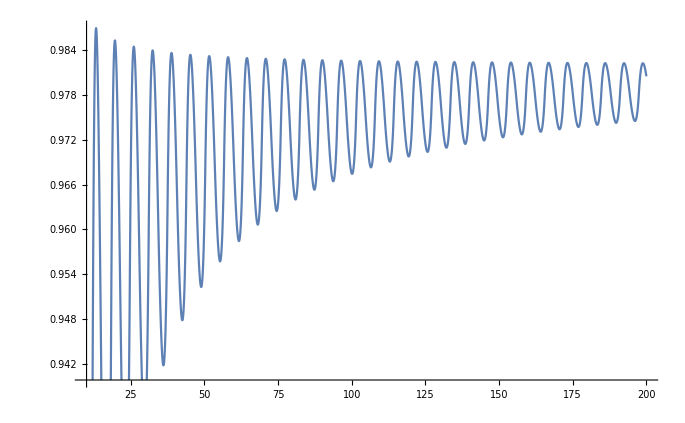
{2444.87,-Graphics-}

```mathematica
Plot[N[NIntegrate[ND[ysol5[1.3,0][t],t,x],{x, 0, g},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/g],{g,10,200}]//AbsoluteTiming
```

```mathematica
Table[N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 150},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/150]//AbsoluteTiming,{a,1.001,2,0.02}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{62.4304,{{0.111712,0.0511224},{0.399165,0.185713},{0.544655,0.271641},{0.617589,0.345712},{0.579237,0.392893},{0.720271,0.46049},{0.905374,0.507968},{0.806987,0.550398},{0.856418,0.591005},{1.02784,0.628284},{0.927298,0.655986},{1.00839,0.686936},{0.942388,0.724696},{0.954262,0.763643},{1.10825,0.801004},{1.11366,0.82481},{1.03345,0.852203},{1.22475,0.889247},{1.23496,0.923703},{1.96776,0.941357},{1.62775,0.97473},{1.20547,1.00981},{1.33858,1.02784},{1.23659,1.05874},{1.35175,1.09273},{2.02643,1.10954},{1.52078,1.14137},{1.51897,1.17233},{1.50441,1.18932},{1.47006,1.22264},{1.38565,1.24537},{1.41006,1.26923},{1.30608,1.30135},{1.20714,1.31739},{1.5102,1.34886},{1.5007,1.37181},{1.38093,1.39474},{1.49308,1.42532},{1.90677,1.44141},{1.42584,1.47273},{1.41107,1.4912},{1.39382,1.51819},{1.41656,1.54389},{1.38282,1.5634},{1.15832,1.59331},{1.4282,1.60929},{1.58284,1.63953},{1.77247,1.65683},{1.52792,1.68444},{1.94436,1.70626}}}

```mathematica
Table[N[NIntegrate[ND[ysol4[a,0][t],t,x],{x, 0, 150},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/150]//AbsoluteTiming,{a,1.001,2,0.02}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{50.4653,{{0.223201,0.0590802},{0.366473,0.226688},{0.593476,0.310835},{0.666057,0.39057},{0.579209,0.43634},{0.524541,0.480727},{0.852728,0.537395},{0.783421,0.582314},{0.897653,0.6205},{0.910636,0.651976},{0.896013,0.688881},{0.785311,0.728771},{0.748054,0.767561},{0.921294,0.803104},{0.922792,0.830379},{0.878604,0.856044},{0.934483,0.89349},{1.05924,0.92638},{0.887034,0.946475},{0.898275,0.979166},{1.28963,1.01273},{1.09513,1.03447},{0.971083,1.06302},{1.00437,1.09541},{1.12889,1.11449},{1.09464,1.14534},{0.988904,1.17489},{1.09003,1.19222},{0.995886,1.22573},{1.14712,1.24995},{1.20167,1.2728},{1.06072,1.30304},{1.16017,1.31924},{1.07023,1.35152},{1.1245,1.37496},{1.10643,1.39778},{1.3202,1.42616},{1.12031,1.44319},{1.15404,1.47418},{1.19985,1.49337},{1.1746,1.52039},{1.26037,1.54451},{1.26308,1.56557},{1.20006,1.593},{1.2661,1.61028},{1.30763,1.63975},{1.53352,1.65664},{1.19984,1.68536},{1.2637,1.70603},{1.34386,1.73021}}}

```mathematica
Table[N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 150},MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0}]/150]//AbsoluteTiming,{a,1.001,2,0.02}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{91.5916,{{0.751918,0.261666},{1.13414,0.42942},{1.0428,0.511585},{1.19457,0.556324},{1.17075,0.602382},{1.30926,0.645972},{1.3062,0.685837},{1.26512,0.724769},{1.34819,0.764502},{1.4678,0.803257},{1.465,0.834323},{1.90663,0.8561},{1.5964,0.890674},{2.02295,0.926691},{1.64772,0.947579},{1.74507,0.975764},{1.74495,1.01103},{1.62642,1.03088},{3.0966,1.05883},{1.65767,1.09176},{1.90263,1.10901},{1.84937,1.14055},{1.67302,1.16697},{1.84362,1.18682},{1.88168,1.21923},{1.71238,1.2364},{1.95372,1.26605},{1.86896,1.29024},{1.87517,1.31127},{2.03206,1.34134},{1.90124,1.35791},{1.91972,1.3885},{1.87957,1.40632},{1.9783,1.43368},{2.05848,1.45652},{2.0286,1.47805},{2.15383,1.50544},{2.06568,1.52293},{2.09164,1.55207},{2.10992,1.56844},{2.04949,1.59732},{2.06729,1.61451},{2.50745,1.6417},{2.1391,1.66104},{2.16156,1.68549},{2.22212,1.70791},{2.25079,1.72902},{2.26577,1.75403},{2.37178,1.77267},{2.27616,1.79919}}}

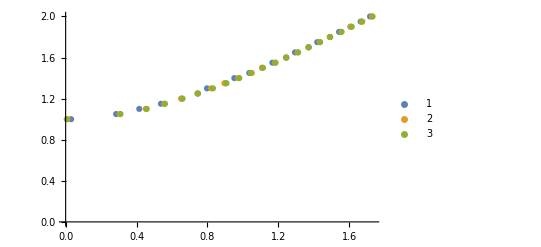
{94.0929,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 50},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/50],a},{a,1,2,0.05}],Table[{N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 150},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/150],a},{a,1,2,0.05}],Table[{N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 250},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/250],a},{a,1,2,0.05}]},PlotLegends->Automatic]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

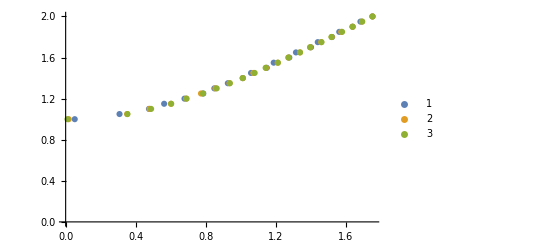
{69.8133,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol4[a,1,0][t],t,x],{x, 0, 50},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/50],a},{a,1,2,0.05}],Table[{N[NIntegrate[ND[ysol4[a,1,0][t],t,x],{x, 0, 150},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/150],a},{a,1,2,0.05}],Table[{N[NIntegrate[ND[ysol4[a,1,0][t],t,x],{x, 0, 250},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/250],a},{a,1,2,0.05}]},PlotLegends->Automatic]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

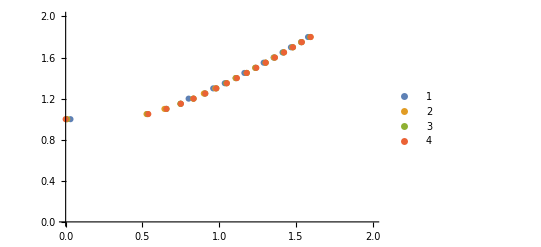
{94.3944,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 50},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/50],a},{a,1,1.8,0.05}],Table[{N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 150},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/150],a},{a,1,1.8,0.05}],Table[{N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 250},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/250],a},{a,1,1.8,0.05}],Table[{2*(Log[(a+1)/(a-1)])^(-1),a},{a,1,1.8,0.05}]},PlotLegends->Automatic,PlotRange->{{0,2},{0,2}}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

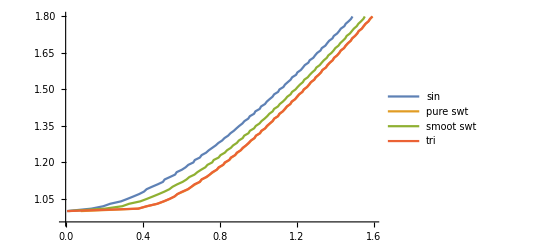
{587.04,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}],Table[{N[NIntegrate[ND[ysol3[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}],Table[{N[NIntegrate[ND[ysol4[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}],Table[{N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}],Table[{a,a+0.5},{a,0,3,0.02}],Table[{a,a},{a,0,3,0.02}]},PlotLegends->{"sin","pure swt","smoot swt","tri"}, Joined->True,PlotRange->{{0,3},{0,3}}]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

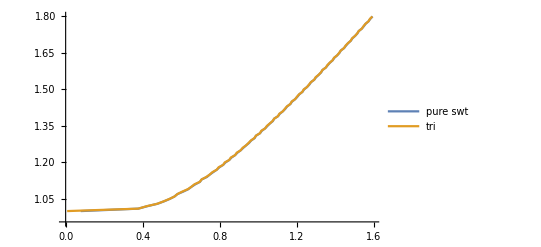
{346.97,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol3[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}],Table[{N[NIntegrate[ND[ysol5[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,1.8,0.01}]},PlotLegends->{"pure swt","tri"}, Joined->True]//AbsoluteTiming
```

```mathematica
Model defined by Deaver and Pierce (distorted sinusoidal CPR)
This equation derive the Current phase relation by solving the equation (1) in the paper (inverse function of θ[I])
```

```mathematica
v[ϕ_,l_?NumericQ]:=FindRoot[s==Sin[ϕ-(l*(2*Pi)*s)],{s,ϕ,l}][[1,2]]
```

```mathematica
N[v[(1.2)*Pi,1.2]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.06794

```mathematica
Manipulate[Plot[{v[θ,l],Sin[θ]},{θ,0,2Pi}],{l,0,8}]
```

```mathematica
Deaver and Pierce CPR
```

```mathematica
ysol6=ParametricNDSolveValue[{a==v[ϕ[t],l]+ϕ'[t],ϕ[0]==0},ϕ,{t,0,1000},{a,l}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol6[a,l][t],t,x]}, {x, 0.000001,20}],{a,0.0001,10},{l,0,1}]
```

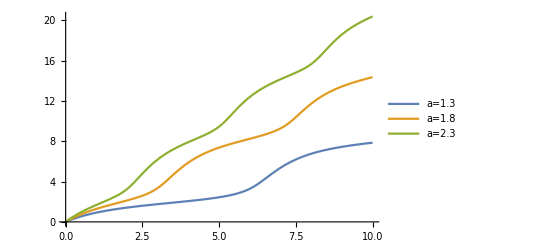
{19.1748,-Graphics-}

```mathematica
Plot[{ysol6[1.3,0.05][x],ysol6[1.8,0.05][x],ysol6[2.3,0.05][x]},{x,0,10},PlotLegends->{"a=1.3","a=1.8","a=2.3"}]//AbsoluteTiming
```

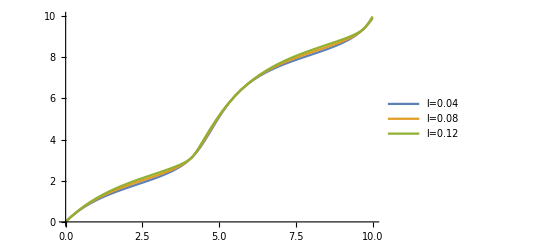
{17.1851,-Graphics-}

```mathematica
Plot[{ysol6[1.5,0.04][x],ysol6[1.5,0.08][x],ysol6[1.5,0.12][x]},{x,0,10},PlotLegends->{"l=0.04","l=0.08","l=0.12"}]//AbsoluteTiming
```

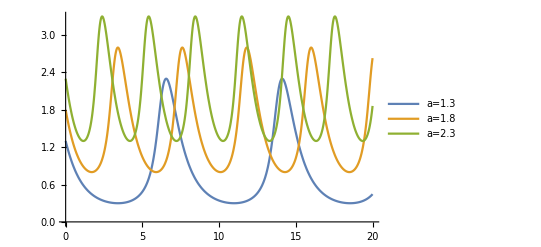
{1.48943,-Graphics-}

```mathematica
Plot[{ND[ysol6[1.3,0.05][t],t,x],ND[ysol6[1.8,0.05][t],t,x],ND[ysol6[2.3,0.05][t],t,x]},{x,0,20},PlotLegends->{"a=1.3","a=1.8","a=2.3"}]//AbsoluteTiming
```

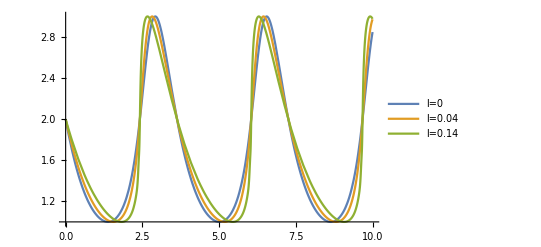
{1.22681,-Graphics-}

```mathematica
Plot[{ND[ysol6[2,0.04][t],t,x],ND[ysol6[2,0.08][t],t,x],ND[ysol6[2,0.14][t],t,x]},{x,0,10},PlotLegends->{"l=0","l=0.04","l=0.14"}]//AbsoluteTiming
```

```mathematica
N[ysol6[1,0][5]]
```

1.2405

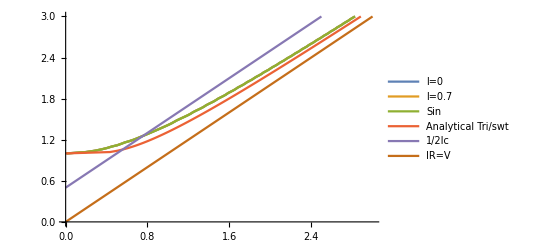
{2609.23,-Graphics-}

```mathematica
ListPlot[{Table[{N[NIntegrate[ND[ysol2[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,3,0.02}],Table[{N[NIntegrate[ND[ysol6[a,0][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,3,0.02}],Table[{N[NIntegrate[ND[ysol6[a,0.12][t],t,x],{x, 0, 200},MaxRecursion->25,Method->{Automatic,"SymbolicProcessing"->0}]/200],a},{a,1,3,0.02}],Table[{(2*(Log[(a+1)/(a-1)])^(-1)),a},{a,0,3,0.02}],Table[{a,a+0.5},{a,0,3,0.02}],Table[{a,a},{a,0,3,0.02}]},PlotLegends->{"l=0","l=0.7","Sin","Analytical Tri/swt","1/2Ic","IR=V"},Joined->True,PlotRange->{{0,3},{0,3}}]//AbsoluteTiming
```

```mathematica
Analitical expression for IV cures for different CPR (found in different papers).
```

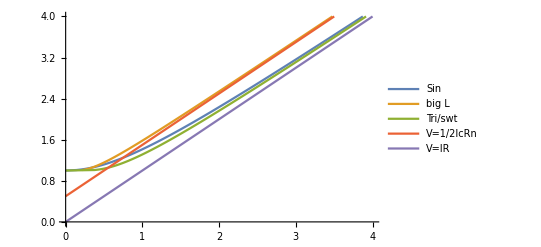
{4.83375,-Graphics-}

```mathematica
ListPlot[{Table[{NIntegrate[A[t,a,0], {t, 10, 10+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->20]/(2*Pi*((√(a^2-1))^-1)),a},{a,1,8,0.01}],Table[{(-1/Log[1-(1/a)]),a},{a,1,8,0.01}],Table[{(2*(Log[(a+1)/(a-1)])^(-1)),a},{a,0,8,0.01}],Table[{a,a+0.5},{a,0,8,0.01}],Table[{a,a},{a,0,8,0.01}]},PlotLegends->{"Sin","big L","Tri/swt","V=1/2IcRn","V=IR"},Joined->True,PlotRange->{{0,4},{0,4}}]//AbsoluteTiming
```

```mathematica
Analitical expression for IV cures for CPR found by Jackel with different critical angles
```

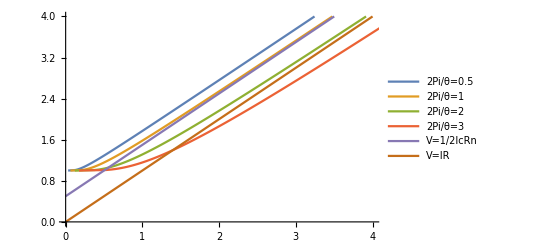
{0.345624,-Graphics-}

```mathematica
ListPlot[{Table[{-(0.5)*((Log[(a-1)/(a-1+0.5)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{-(1)*((Log[(a-1)/(a-1+1)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{-(2)*((Log[(a-1)/(a-1+2)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{-(3)*((Log[(a-1)/(a-1+3)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{a,a+0.5},{a,0,8,0.01}],Table[{a,a},{a,0,8,0.01}]},PlotLegends->{"2Pi/θ=0.5","2Pi/θ=1","2Pi/θ=2","2Pi/θ=3","V=1/2IcRn","V=IR"},Joined->True,PlotRange->{{0,4},{0,4}}]//AbsoluteTiming
```

```mathematica
Comparison analitical expression for IV cures for CPR found by Jackel with different critical angles and other CPR
```

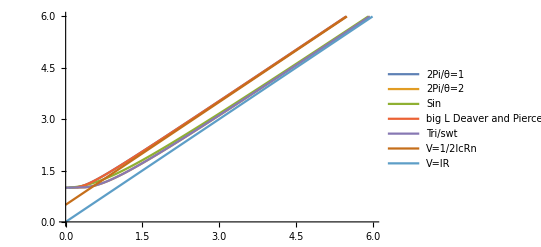
{4.08052,-Graphics-}

```mathematica
ListPlot[{Table[{-(1)*((Log[(a-1)/(a-1+1)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{-(2)*((Log[(a-1)/(a-1+2)])^(-1)),a},{a,1.0000001,8,0.01}],Table[{NIntegrate[A[t,a,0], {t, 10, 10+(2*Pi*((√(a^2-1))^-1))},MaxRecursion->20]/(2*Pi*((√(a^2-1))^-1)),a},{a,1,8,0.01}],Table[{(-1/Log[1-(1/a)]),a},{a,1,8,0.01}],Table[{(2*(Log[(a+1)/(a-1)])^(-1)),a},{a,0,8,0.01}],Table[{a,a+0.5},{a,0,8,0.01}],Table[{a,a},{a,0,8,0.01}]},PlotLegends->{"2Pi/θ=1","2Pi/θ=2","Sin","big L Deaver and Pierce","Tri/swt","V=1/2IcRn","V=IR"},Joined->True,PlotRange->{{0,6},{0,6}}]//AbsoluteTiming
```